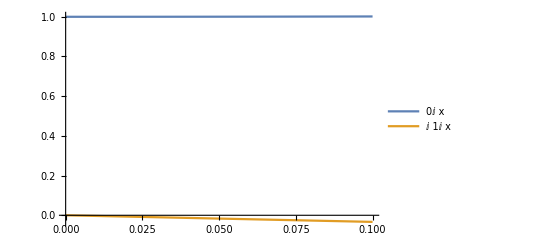

```mathematica
Plot[{SphericalBesselJ[0,I x],I SphericalBesselJ[1,I x],I^2 SphericalBesselJ[1,I x]},{x,0,0.1},PlotLegends->"Expressions"]
```

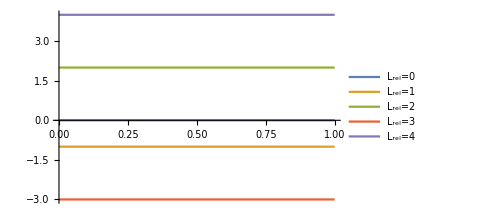

```mathematica
Plot[Evaluate[Table[n Sign[I^n SphericalBesselJ[n,I x]],{n,0,4}]],{x,0.001,1},PlotLegends->Table["L_rel="<>ToString[n-1],{n,100}],ImageSize->Medium]
```